# Initialisation

fixed parameters

```mathematica
ClearAll[Ip,ω,r]
Ip=0.5;
ω = 0.057;
r={π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}
```

{π/4,π/5,π/6,π/7,π/8,π/9,π/10,π/11,π/12,π/16,π/20,π/24,π/28,π/36,π/45,π/50,π/60,π/70,π/80,π/90,π/120,π/140,π/180,0}

function definitions

```mathematica
ClearAll[E1,A, Sf,Sfunc, DsFunc]
(*Define the electric field function and the vector potential*)
E1[t_]:=Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2t];
A[tx_]=-Integrate[E1[t],t]/. t->tx;

(*Define Sf,Sfunc,and DsFunc*)
Sf[ty_,p_]=Integrate[2 p*A[t]+(A[t])^2,t]/. t->ty;
Sfunc[t_,p_]:=0.5*Sf[t,p]+(0.5*p^2+Ip)*t;
DsFunc[t_,p_]:=D[Sfunc[tz,p],tz]/. tz->t;
```

define momentum grid

```mathematica
ClearAll[pxValues]
(*Define the range for px and py values*)
pxValues=Range[-3,3,0.1];
Print[Length[pxValues]]
```

61

define plotting functions

```mathematica
ClearAll[plotEx,plotRoots](*Plot Ex  and roots*)
plotEx:=Quiet[Plot[E1[t],{t,realMin,realMax},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]]

plotRoots[filteredTValues_]:=Quiet[ListPlot[{{Re[#],E1[Re[#]][[1]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large]];
```

create grid of seeds

```mathematica
ClearAll[realMax,realMin,imagMax,imagMin,realSteps,imagSteps,listofseeds,initialGuess,listofseeds,seedPoints](*Generate the grid of seeds*) 

(*pick realmin to realmax as the range to capture the 4 saddle points in a periodic range of 2Pi*)
realMin=-2.133;realMax=4.150;
imagMin=0;imagMax=5;
realSteps=10;imagSteps=10;

listofseeds=Flatten[Table[x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}],1];

(*(*Add the specific initial guess to the list of seeds*)
initialGuess=-2.0334+1.2321 ⅈ;
listofseeds=Prepend[listofseeds,initialGuess];

(*Ensure seeds are numerical values*)
listofseeds=N[listofseeds];

(*Extract real and imaginary parts of the seeds*)
seedPoints={Re[#],Im[#]}&/@listofseeds;*)
```

find all the roots for all values of px (saddle point solutions)

```mathematica
ClearAll[generatePlotAndRoots];

(*Function to generate plots and roots for a given p*)
generatePlotAndRoots[p_]:=
Module[
{allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues},

(*Find roots*)
allSolutions=Round[t/. Quiet[
Table[
FindRoot[DsFunc[t,p]==0,{t,tseed}],
{tseed,listofseeds}]
],0.0001];

complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];

(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#,p]]]<=tolerance&&Abs[Im[DsFunc[#,p]]]<=tolerance&];

(*Return both the plot and filteredTValues*)
{filteredTValues}];
```

# Calculation of saddle point solutions!

```mathematica
(*Generate results using the precise pValues*)
results=Table[
generatePlotAndRoots[p],{p,pxValues}
]
```

{{{-2.0008+1.2825 ⅈ,0.4965+1.6343 ⅈ,0.7616+1.589 ⅈ,3.8842+1.2373 ⅈ}},{{-1.9913+1.2652 ⅈ,0.4907+1.6225 ⅈ,0.7634+1.5754 ⅈ,3.8789+1.218 ⅈ}},{{-1.9812+1.2474 ⅈ,0.4845+1.6106 ⅈ,0.7652+1.5613 ⅈ,3.873+1.1981 ⅈ}},{{-1.9704+1.2292 ⅈ,0.478+1.5984 ⅈ,0.7673+1.5469 ⅈ,3.8666+1.1776 ⅈ}},{{-1.9588+1.2104 ⅈ,0.4712+1.5859 ⅈ,0.7695+1.532 ⅈ,3.8597+1.1565 ⅈ}},{{-1.9464+1.1911 ⅈ,0.464+1.5731 ⅈ,0.7719+1.5166 ⅈ,3.852+1.1346 ⅈ}},{{-1.933+1.1714 ⅈ,0.4564+1.5601 ⅈ,0.7745+1.5008 ⅈ,3.8437+1.1121 ⅈ}},{{-1.9186+1.1511 ⅈ,0.4484+1.5468 ⅈ,0.7774+1.4844 ⅈ,3.8344+1.0888 ⅈ}},{{-1.9031+1.1304 ⅈ,0.4399+1.5332 ⅈ,0.7806+1.4675 ⅈ,3.8243+1.0648 ⅈ}},{{-1.8863+1.1092 ⅈ,0.4308+1.5193 ⅈ,0.7841+1.4501 ⅈ,3.813+1.04 ⅈ}},{{-1.8681+1.0876 ⅈ,0.4212+1.5051 ⅈ,0.7879+1.432 ⅈ,3.8006+1.0145 ⅈ}},{{-1.8483+1.0656 ⅈ,0.411+1.4906 ⅈ,0.7921+1.4133 ⅈ,3.7868+0.9883 ⅈ}},{{-1.8268+1.0433 ⅈ,0.4001+1.4758 ⅈ,0.7968+1.3939 ⅈ,3.7715+0.9614 ⅈ}},{{-1.8033+1.0209 ⅈ,0.3884+1.4608 ⅈ,0.802+1.3737 ⅈ,3.7545+0.9339 ⅈ}},{{-1.7777+0.9985 ⅈ,0.376+1.4455 ⅈ,0.8078+1.3529 ⅈ,3.7355+0.9059 ⅈ}},{{-1.7498+0.9764 ⅈ,0.3626+1.43 ⅈ,0.8143+1.3312 ⅈ,3.7145+0.8776 ⅈ}},{{-1.7194+0.9547 ⅈ,0.3483+1.4142 ⅈ,0.8215+1.3086 ⅈ,3.6912+0.8491 ⅈ}},{{-1.6863+0.934 ⅈ,0.3329+1.3984 ⅈ,0.8297+1.2852 ⅈ,3.6654+0.8208 ⅈ}},{{-1.6505+0.9145 ⅈ,0.3163+1.3824 ⅈ,0.8388+1.2609 ⅈ,3.637+0.793 ⅈ}},{{-1.612+0.8968 ⅈ,0.2984+1.3664 ⅈ,0.8492+1.2356 ⅈ,3.606+0.766 ⅈ}},{{-1.5708+0.8814 ⅈ,0.2791+1.3506 ⅈ,0.8609+1.2094 ⅈ,3.5724+0.7402 ⅈ}},{{-1.5272+0.8687 ⅈ,0.2583+1.335 ⅈ,0.8743+1.1824 ⅈ,3.5362+0.716 ⅈ}},{{-1.4815+0.8593 ⅈ,0.2359+1.3199 ⅈ,0.8894+1.1544 ⅈ,3.4978+0.6938 ⅈ}},{{-1.4342+0.8535 ⅈ,0.2118+1.3054 ⅈ,0.9067+1.1257 ⅈ,3.4573+0.6738 ⅈ}},{{-1.3858+0.8517 ⅈ,0.186+1.2919 ⅈ,0.9263+1.0964 ⅈ,3.4151+0.6563 ⅈ}},{{-1.3369+0.8542 ⅈ,0.1584+1.2796 ⅈ,0.9487+1.0668 ⅈ,3.3714+0.6414 ⅈ}},{{-1.2882+0.8609 ⅈ,0.1292+1.2688 ⅈ,0.974+1.0371 ⅈ,3.3267+0.6292 ⅈ}},{{-1.2403+0.8719 ⅈ,0.0984+1.26 ⅈ,1.0024+1.0078 ⅈ,3.2811+0.6197 ⅈ}},{{-1.1939+0.8869 ⅈ,0.0664+1.2533 ⅈ,1.0343+0.9794 ⅈ,3.2349+0.613 ⅈ}},{{-1.1497+0.9057 ⅈ,0.0334+1.2493 ⅈ,1.0695+0.9525 ⅈ,3.1883+0.6089 ⅈ}},{{-1.1081+0.9277 ⅈ,0.+1.2479 ⅈ,1.1081+0.9277 ⅈ,3.1416+0.6076 ⅈ}},{{-1.0695+0.9525 ⅈ,-0.0334+1.2493 ⅈ,1.1497+0.9057 ⅈ,3.0949+0.6089 ⅈ}},{{-1.0343+0.9794 ⅈ,-0.0664+1.2533 ⅈ,1.1939+0.8869 ⅈ,3.0483+0.613 ⅈ}},{{-1.0024+1.0078 ⅈ,-0.0984+1.26 ⅈ,1.2403+0.8719 ⅈ,3.0021+0.6197 ⅈ}},{{-0.974+1.0371 ⅈ,-0.1292+1.2688 ⅈ,1.2882+0.8609 ⅈ,2.9565+0.6292 ⅈ}},{{-0.9487+1.0668 ⅈ,-0.1584+1.2796 ⅈ,1.3369+0.8542 ⅈ,2.9118+0.6414 ⅈ}},{{-0.9263+1.0964 ⅈ,-0.186+1.2919 ⅈ,1.3858+0.8517 ⅈ,2.8681+0.6563 ⅈ}},{{-0.9067+1.1257 ⅈ,-0.2118+1.3054 ⅈ,1.4342+0.8535 ⅈ,2.8259+0.6738 ⅈ}},{{-0.8894+1.1544 ⅈ,-0.2359+1.3199 ⅈ,1.4815+0.8593 ⅈ,2.7854+0.6938 ⅈ}},{{-0.8743+1.1824 ⅈ,-0.2583+1.335 ⅈ,1.5272+0.8687 ⅈ,2.7469+0.716 ⅈ}},{{-0.8609+1.2094 ⅈ,-0.2791+1.3506 ⅈ,1.5708+0.8814 ⅈ,2.7108+0.7402 ⅈ}},{{-0.8492+1.2356 ⅈ,-0.2984+1.3664 ⅈ,1.612+0.8968 ⅈ,2.6772+0.766 ⅈ}},{{-0.8388+1.2609 ⅈ,-0.3163+1.3824 ⅈ,1.6505+0.9145 ⅈ,2.6462+0.793 ⅈ}},{{-0.8297+1.2852 ⅈ,-0.3329+1.3984 ⅈ,1.6863+0.934 ⅈ,2.6178+0.8208 ⅈ}},{{-0.8215+1.3086 ⅈ,-0.3483+1.4142 ⅈ,1.7194+0.9547 ⅈ,2.592+0.8491 ⅈ}},{{-0.8143+1.3312 ⅈ,-0.3626+1.43 ⅈ,1.7498+0.9764 ⅈ,2.5687+0.8776 ⅈ}},{{-0.8078+1.3529 ⅈ,-0.376+1.4455 ⅈ,1.7777+0.9985 ⅈ,2.5477+0.9059 ⅈ}},{{-0.802+1.3737 ⅈ,-0.3884+1.4608 ⅈ,1.8033+1.0209 ⅈ,2.5287+0.9339 ⅈ}},{{-0.7968+1.3939 ⅈ,-0.4001+1.4758 ⅈ,1.8268+1.0433 ⅈ,2.5117+0.9614 ⅈ}},{{-0.7921+1.4133 ⅈ,-0.411+1.4906 ⅈ,1.8483+1.0656 ⅈ,2.4964+0.9883 ⅈ}},{{-0.7879+1.432 ⅈ,-0.4212+1.5051 ⅈ,1.8681+1.0876 ⅈ,2.4826+1.0145 ⅈ}},{{-0.7841+1.4501 ⅈ,-0.4308+1.5193 ⅈ,1.8863+1.1092 ⅈ,2.4701+1.04 ⅈ}},{{-0.7806+1.4675 ⅈ,-0.4399+1.5332 ⅈ,1.9031+1.1304 ⅈ,2.4589+1.0648 ⅈ}},{{-0.7774+1.4844 ⅈ,-0.4484+1.5468 ⅈ,1.9186+1.1511 ⅈ,2.4487+1.0888 ⅈ}},{{-0.7745+1.5008 ⅈ,-0.4564+1.5601 ⅈ,1.933+1.1714 ⅈ,2.4395+1.1121 ⅈ}},{{-0.7719+1.5166 ⅈ,-0.464+1.5731 ⅈ,1.9464+1.1911 ⅈ,2.4311+1.1346 ⅈ}},{{-0.7695+1.532 ⅈ,-0.4712+1.5859 ⅈ,1.9588+1.2104 ⅈ,2.4235+1.1565 ⅈ}},{{-0.7673+1.5469 ⅈ,-0.478+1.5984 ⅈ,1.9704+1.2292 ⅈ,2.4165+1.1776 ⅈ}},{{-0.7652+1.5613 ⅈ,-0.4845+1.6106 ⅈ,1.9812+1.2474 ⅈ,2.4102+1.1981 ⅈ}},{{-0.7634+1.5754 ⅈ,-0.4907+1.6225 ⅈ,1.9913+1.2652 ⅈ,2.4043+1.218 ⅈ}},{{-0.7616+1.589 ⅈ,-0.4965+1.6343 ⅈ,2.0008+1.2825 ⅈ,2.3989+1.2373 ⅈ}}}

```mathematica
Print[Length[results]]
Print[Length[pxValues]]
```

61

61

# Plotting electric field with saddle point solutions for corresponding px Momenta

```mathematica
Manipulate[
plotData=generatePlotAndRoots[px];
filteredTValues=plotData[[1]];
plotRoots=ListPlot[{{Re[#],E1[Re[#]]}&/@filteredTValues},PlotStyle->{Red,PointSize[0.02]},AxesLabel->{"Time, t","Electric Field Ex"},ImageSize->Large];

Show[plotEx,plotRoots,PlotRange->All,PlotLabel->"px = "<>ToString[px]],{{px,0,"Momentum px"},-3,3,0.1}]
```

# Rearranging data structure for time arrays

```mathematica
ClearAll[newResults,tsExtended,validData,realAndImagTimes,colorFunction,coloredPoints];

newResults=Table[
{pValue=-3+(i-1)*0.1,results[[i,1]]},
{i,Length[results]}
];

tsExtended=Map[
Join[
{#[[1]]},PadRight[#[[2]],4,Null]
]&,newResults];

(*Filter and prepare the data for further processing*)
validData=Select[
Flatten[
Table[
If[
tsExtended[[i,j+1]]=!=Null,
{Re[tsExtended[[i,j+1]]],Im[tsExtended[[i,j+1]]],tsExtended[[i,1]]},
Nothing],
{i,Length[tsExtended]},
{j,1,4}]
,1],
#[[1]]=!=Null&];

(*Extract real and imaginary times*)
realAndImagTimes=validData[[All,1;;2]];

colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Generate a list of colored points with the custom color function*)
coloredPoints=Table[
{colorFunction[validData[[i,3]]]
,Point[validData[[i,1;;2]]]
},
{i,1,Length[validData]}
];
```

# plotting saddle points complex plane (px rainbow scale)

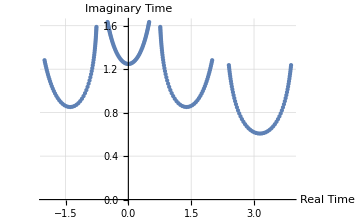

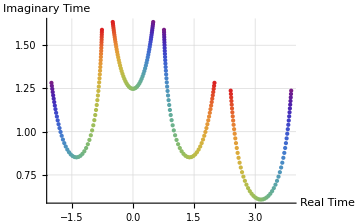

```mathematica
(*Plot the 2D graph*)
ListPlot[
realAndImagTimes,

AxesLabel->{"Real Time","Imaginary Time"},
PlotStyle->PointSize[Medium],
GridLines->Automatic,
ImageSize->Medium]

(*Plot the 2D graph with the custom color grading for momentum*)
Show[
Graphics[
{coloredPoints},

Axes->True,
AxesLabel->{"Real Time","Imaginary Time"},
GridLines->Automatic],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/GoldenRatio]
```

# Calculating & plotting 2D real trajectories inside the tunnel (ReX vs ReT)

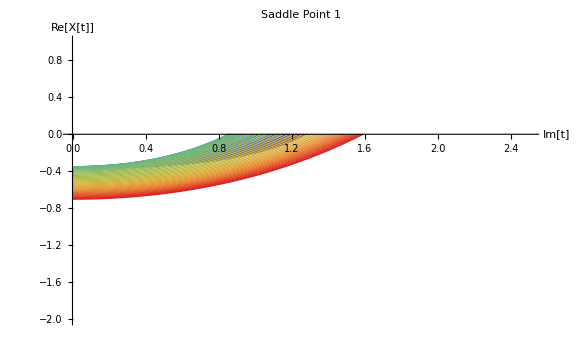
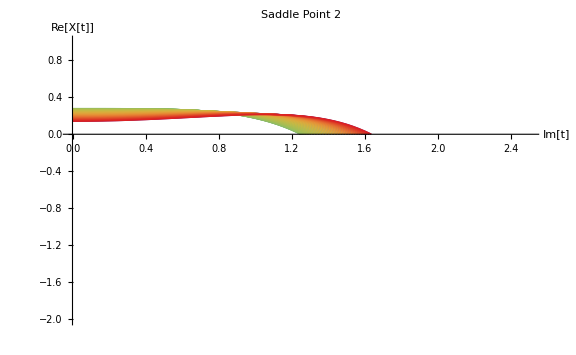
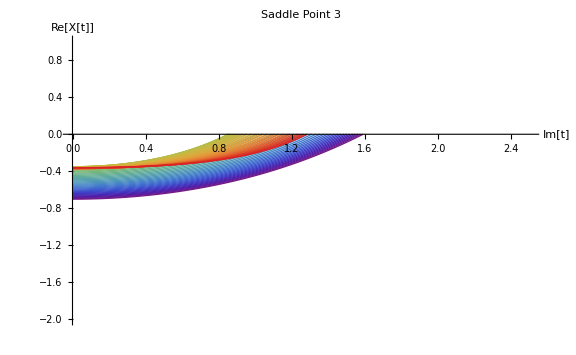
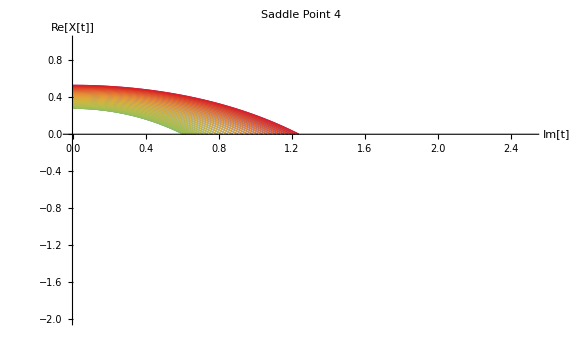

```mathematica
ClearAll[X1, X, fixedPlotRange,imaginaryPlots, combinedImaginaryPlots];

X1[t_,p_]=Evaluate[Integrate[p+A[t],t]];
X[t_,p_,ts_]:=X1[t,p]-X1[ts,p];
(*Real trajectory vs Imaginary time*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Define a fixed plot range for comparison*)
fixedPlotRange={{0,2.5},{-2,1}}; 

(*Collect individual plots for each saddle point*)
imaginaryPlots=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[Re[X[Re[tsExtended[[k,i]]]+I ti,p,tsExtended[[k,i]]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->(*All*)fixedPlotRange,
AxesLabel->{"Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p],
ImageSize->Large]
],
{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots=
Table[
Show[
imaginaryPlots[[All,i]],

PlotRange->(*All*)fixedPlotRange,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];
combinedImaginaryPlots
```

# Calculating & plotting 3D real trajectories inside & outside the tunnel (ReX vs ImT vs ReT)

```mathematica
ClearAll[threeDPlots,combinedThreeDPlots];
(*3D plot of the whole trajectory inside and outside the tunnel, ReX vs ReT vs ImT*)
(*Collect individual plots for each saddle point*)
threeDPlots=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]],

ParametricPlot3D[
{Re[tr+I ti],Im[tr+I ti],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. ti->0.,
{tr,Re[tsExtended[[k,i]]],Re[tsExtended[[k,i]]]+2 Pi},

PlotRange->All,
AxesLabel->{"Re[t]","Im[t]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}]
],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots=
Table[
Show[
threeDPlots[[All,i]],

PlotRange-> All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

# Calculating & plotting 3D real & imaginary trajectories inside the tunnel (ReX vs ImX vs ImT)

```mathematica
ClearAll[threeDPlots2,combinedThreeDPlots2];
(*3D plot of real and imaginary trajectories against imaginary time*)
(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[X[tr+I ti,p,tsExtended[[k,i]]]],Re[X[tr+I ti,p,tsExtended[[k,i]]]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[X[t]]","Re[X[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[
Show[
threeDPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange-> All]
```

-Graphics3D-

# Calculating & plotting 2D real velocities inside the tunnel (ReV vs ImT)

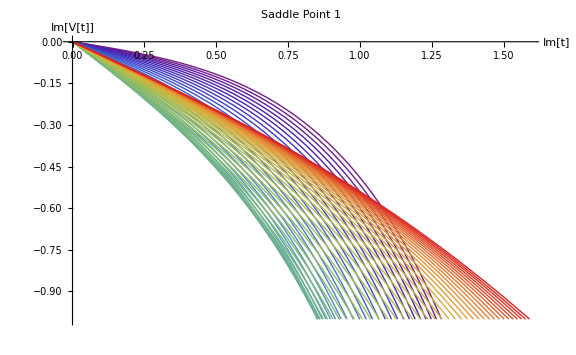
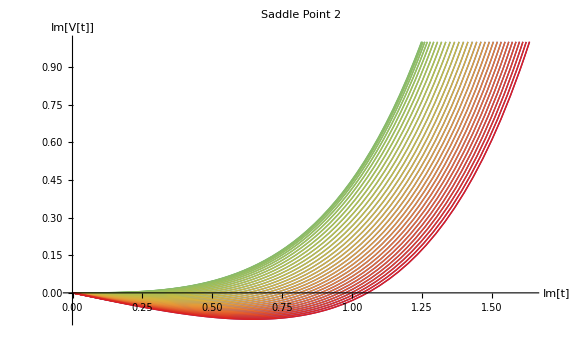
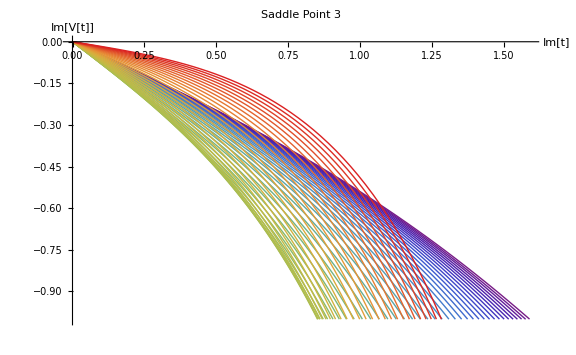
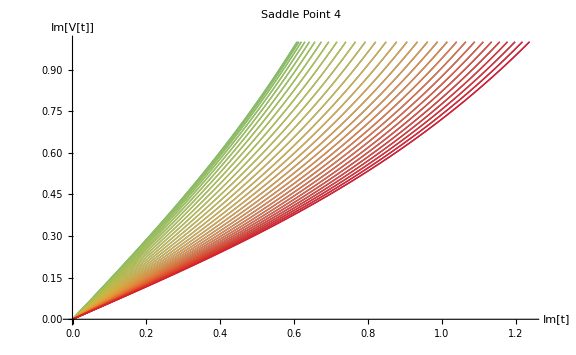

```mathematica
ClearAll[V1,imaginaryPlots2, combinedImaginaryPlots2];
(*Imaginary Velocity vs Imaginary time*)
V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[Im[V1[Re[tsExtended[[k,i]]]+I ti,p]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedImaginaryPlots2=
Table[
Show[
imaginaryPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)

combinedImaginaryPlots2
```

# Calculating & plotting 3D real & imaginary velocities inside the tunnel (ReV vs ImV vs ImT)

```mathematica
(*3D plot of real and imaginary velocities against imaginary time*)

ClearAll[V1,threeDPlots2, combinedThreeDPlots2];

V1[t_,p_]:=p+A[t];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots2=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[V1[tr+I ti,p]],Re[V1[tr+I ti,p]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[V[t]]","Re[V[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots2=
Table[
Show[
threeDPlots2[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots2
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange-> All]
```

-Graphics3D-

# Calculating & plotting 2D real electric field inside the tunnel (ReE1 vs ImT)

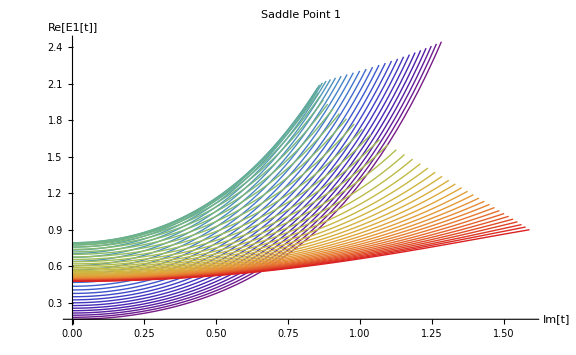
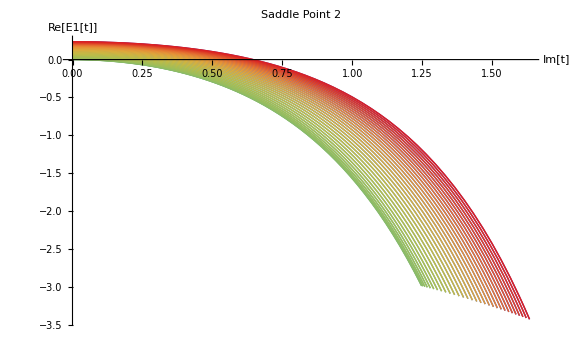
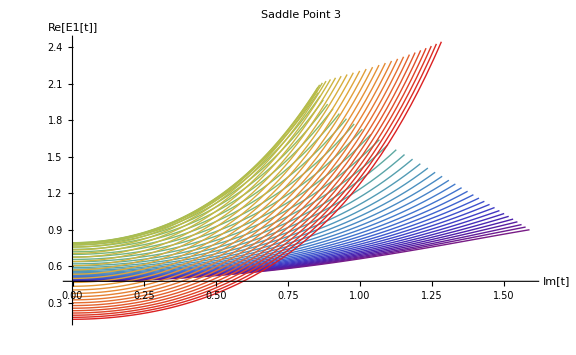
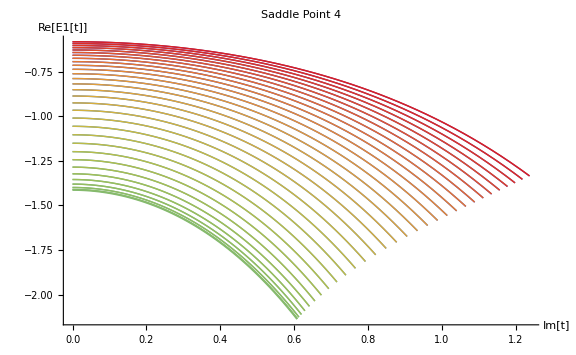

```mathematica
(*Real Electric field for all saddle points (with different moment p) against imaginary time.*)

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
imaginaryPlots1=
Table[
Module[
{p=tsExtended[[k,1]]},
Plot[
Re[E1[Re[tsExtended[[k,i]]]+I ti]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
PlotLabel->"p = "<>ToString[p]]
],
{k,1,Length[tsExtended]},{i,2,5}
];

(*Combine plots for each saddle point*)
combinedImaginaryPlots1=
Table[
Show[
imaginaryPlots1[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large
],
{i,1,4}
];

(*Display combined plots*)
combinedImaginaryPlots1
```

# Calculating & plotting 3D real & imaginary electric field inside the tunnel (ReE1 vs ImE1 vs ImT)

```mathematica
(*3D plot of real and imaginary electric field against imaginary time*)
ClearAll[threeDPlots3, combinedThreeDPlots3];

(*Define a color function for momentum*)
colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]

(*Collect individual plots for each saddle point*)
threeDPlots3=
Table[
Module[
{p=tsExtended[[k,1]]},

Show[
{ParametricPlot3D[
{Im[tr+I ti],Im[E1[Re[tsExtended[[k,i]]]+I ti]],Re[E1[Re[tsExtended[[k,i]]]+I ti]]}
/. tr->Re[tsExtended[[k,i]]],
{ti,Im[tsExtended[[k,i]]],0},

PlotRange->All,
AxesLabel->{"Im[t]","Im[E1[t]]","Re[E1[t]]"},
PlotStyle->{Thick,colorFunction[p]},
Mesh->None,
ColorFunction->Function[{x,y,z},colorFunction[p]],
SphericalRegion->True,
BoxRatios->{1,1,1},
PlotLabel->"p = "<>ToString[p]]}
]],{k,1,Length[tsExtended]},{i,2,5}];

(*Combine plots for each saddle point*)
combinedThreeDPlots3=
Table[
Show[
threeDPlots3[[All,i]],

PlotRange->All,
PlotLabel->"Saddle Point "<>ToString[i],
ImageSize->Large],
{i,1,4}];

(*Display combined plots*)
combinedThreeDPlots3
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Show[%,PlotRange->All]
```

-Graphics3D-